```mathematica
FileNameForTupleBis[primes_] := Module[{fileName, temp, sep, pPos},
    sep = "\\";
    temp = "d:\\triangle\\DataSrc";
    For[pPos = 1, pPos <= Length[primes], pPos++,
      temp = StringJoin[temp, sep, ToString[primes[[pPos]]]];
      ];
    If [Not[DirectoryQ[temp]],
   CreateDirectory[temp]
   ];
    temp = StringJoin[temp, "\\SolutionsBis.txt"];
    fileName = temp;
    Return[fileName]
   ]
```

```mathematica
CalcGoodForTuple2[tuple_, start_,end_] := Module[{sorted,fileName, file, current, index, dummy, range=1000, continue, distance,l=Length[tuple],zero=0,primeIndex=1, attempt=1},
(* always make sure the tuple is sorted *)
sorted = Sort[tuple];
fileName = FileNameForTupleBis[sorted];
index = 0;
current = 0;

(* read any existing good values - actually read the last one and store it in the current variable.   Also increment the index variable *)
If [FileExistsQ[fileName],
Monitor[
continue = True;
file = OpenRead[fileName];
While[continue,
dummy = ReadList[file, Number, range];
index += Length[dummy];
If [Length[dummy] ≠ 0, current = Last[dummy]];
If [current ≥end, continue=False];
If[Length[dummy] ≠ range, continue = False];
];
Close[file];
current +=1;
,
"Reading existing " <> fileName <> " value " <> ToString[index]
]
];
current=Max[start,current];
(* now calculate good values and append them to the file for as long as the bound is not reached *)
(* If the process is aborted, the file is closed *)
file = OpenAppend[fileName, PageWidth->40000];
CheckAbort[
Monitor[
While[current<end,
distance = Distance[current, sorted[[primeIndex]]];
current += distance;
If [distance == 0,
zero+=1;
(*Print[{current,primeIndex,zero,distance}];*)
If[zero==l,
index +=1;
zero=0;
Write[file,current];
current+=1,
attempt=0
],
zero=0
];
attempt+=1;
primeIndex=Mod[primeIndex,l]+1;
]
,
"Calculating good values " <> fileName <> ". " <> ToString[index] <> " found."<> "- " <> ToString[N[Log[10,current],50]] <> "  " <> ToString[attempt]
];
Close[file];
,
Print["Aborted at value : " <> ToString[index] ];
Close[file];
Abort[];
];
]
```

```mathematica
CalcGoodForTuple2[{3,5,7,11},100000,10^2000000]
```

```mathematica
CloseStreams[]
```

```mathematica
Clear[ddd]
```

```mathematica
Timing[ddd=CalcGoodForTuple2[{3,5,7,11},0,10^10000]]
```

{1270.75,{0,«189205»}}

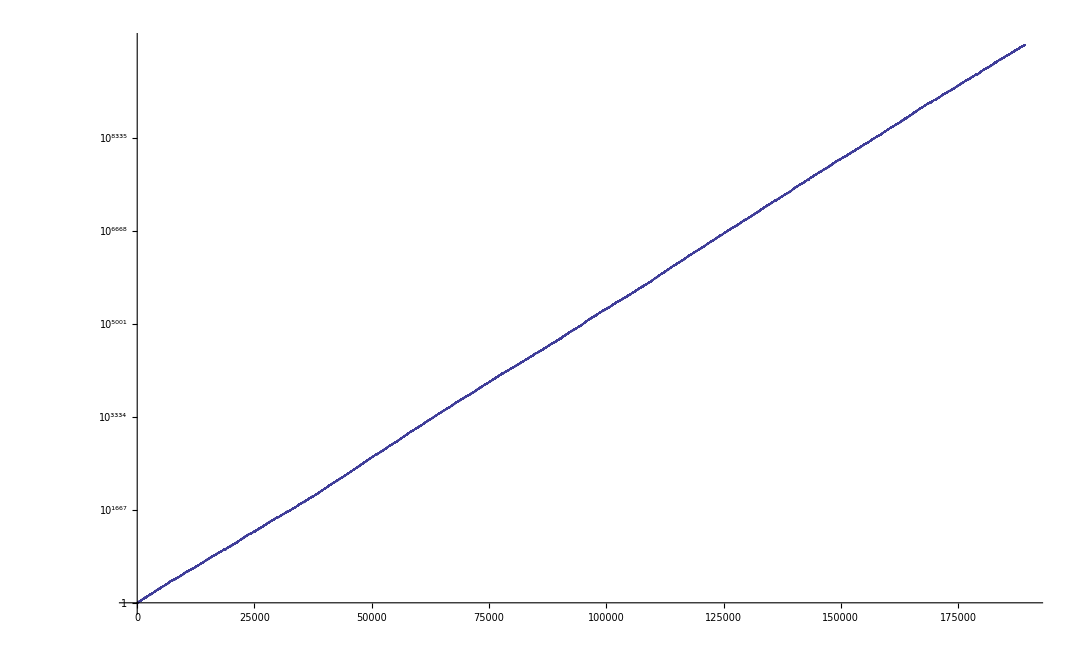

```mathematica
ListLogPlot[ddd,Joined->True]
```

```mathematica
NumberForm[N[Log[10,2^1000]],20]
```

301.0299956639812

```mathematica
ToString[N[Log[10,2^10000]]]
```

3010.3

```mathematica
CalcGoodForTuple2[{7,11,13,17},10^10000,10^200000]
```

Aborted at value : 140

$Aborted

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\17\SolutionsBis.txt.140 found.-2093.8052866032022598929414969532820083014007059442 176266
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\17\SolutionsBis.txt.140 found.-16085.964445385040473162295597944003378126629503872 3812265
```

```mathematica
CalcGoodForTuple2[tuple_, start_,end_] := Module[{sorted,fileName, file, current, index, dummy, range=1000, continue, distance,l=Length[tuple],zero=0,primeIndex=1, attempt=1},
(* always make sure the tuple is sorted *)
sorted = Sort[tuple];
fileName = FileNameForTupleBis[sorted];
index = 0;
current = 0;

(* read any existing good values - actually read the last one and store it in the current variable.   Also increment the index variable *)
If [FileExistsQ[fileName],
Monitor[
continue = True;
file = OpenRead[fileName];
While[continue,
dummy = ReadList[file, Number, range];
index += Length[dummy];
If [Length[dummy] ≠ 0, current = Last[dummy]];
If [current ≥end, continue=False];
If[Length[dummy] ≠ range, continue = False];
];
Close[file];
current +=1;
,
"Reading existing " <> fileName <> " value " <> ToString[index]
]
];
current=Max[start,current];
(* now calculate good values and append them to the file for as long as the bound is not reached *)
(* If the process is aborted, the file is closed *)
file = OpenAppend[fileName, PageWidth->40000];
CheckAbort[
Monitor[
While[current<end,
distance = Distance[current, sorted[[primeIndex]]];
current += distance;
If [distance == 0,
zero+=1;
(*Print[{current,primeIndex,zero,distance}];*)
If[zero==l,
index +=1;
zero=0;
Write[file,current];
current+=1,
attempt=0
],
zero=0
];
attempt+=1;
primeIndex=Mod[primeIndex,l]+1;
]
,
"Calculating good values " <> fileName <> ". " <> ToString[index] <> " found."<> "- " <> ToString[N[Log[10,current],50]] <> "  " <> ToString[attempt]
];
Close[file];
,
Print["Aborted at value : " <> ToString[current] ];
Close[file];
Abort[];
];
]
```

```mathematica
Length[GoodForTuple[{7,11,13,19}]]
```

7546

```mathematica
Timing[ CalcGoodForTuple2[{7,11,13,19},0,10^20000]]
```

Aborted at value : 2370

$Aborted

```mathematica
Timing[ CalcGoodForTuple2[{3,31,43,173,229},827099843745363330595561168673255227577265091281461945985229940354804800132456074710324743857058021008366913362628775322001357792026245915431551864053722509858960778997780453738527196485675354956701111388108392551788226806694012299783739208434819301297676924284456549704355438144170038507361989761573165707509134585929492475122720822032348685659679893064183132286757800613167584439239617325564005254421994838404816647676731833613235643807627570987412195327704876071604030310353590465118871769342722202143006641692084810599215780467188430408046729519225650594656424839748402357856763710225093325835582881304013760539481724349833438320721840532275599331993612761247457758048006822082656761806318262230918919753896093414533967548616863448040549678124134427408563285363901771457961429996933704852465214973294253506547959456581176143216206669151639879010318047316907451852617109434652457304353339134082786895657418007582937813705163326986022675393045010615094259407967538581739185755315407669607978910364950992923570455200395506327042134192630556246520839777632841373360674429866728462220314452239769469963650355763982147535436635364729313238479477394882849195304679683933509008681469066009319964461014698102199906125845138285170138255666209209310187789966740510767780276959831547125972882600634815186965969260107736553696748832535427231453820415907218579444348402949616224961574164092199733740350552172369852219384376618997977111641345832570364764697463591677125174848644178994261631321633880248634581147123271803911746330823017798016182643533840734145816368623933368201303793653365085610477161839780920618227321834018519663185899384059539261305346994842388235698109007434722956598874603759408272552554290881099680325023897651803824593387982170955256316116796615040167046783317749264552067208333551385431737526533365285969246307330310560580639043816333701917954668735721429137639681977265822229694170082344261932835962472509481663816749035285938005154003057879786620978226158617414811081437003871132794494571047653301189861090166207179003156866957179515368417872954232922451214725814618444995574492383655513931749653036727575663930091641722420849775952549940548567496088956507499315127213855901709289097362824917012387882177970039666817862263292773320835994293821750887067533252165758759646000530374234126690923569122467657300836466700631837597671205257464859726113659049239066514690477274345758600308109191644861887545612763580187110299463125011608628173080407778044504158944686832101768298116226505628076944708763663100293462418319274050809910444954469243221665878731948759240209026086810463952846276407152651330656819228535737372579832728721585921141201028270302830323327091945192675835547112373205825879004958145601355536988897173147932609127746657856575720140290020940133525367472224248222657999468437623862971791608692099023432968955667615541210743033265831223026846296353480291627154679975985531409598416686269702614224394070948515382581492336121448165742155116194265383283797004350540149616734777585751376632776086089113382758999124541903509930309467939480605633578650186240186260395821617136071578352976304970833648155640511487068214062370537590363251722222485846947149761254406904972003308260230379605231482108097722701886327805491371235026122233684921575379039193915392626936682199056483064954123329332819898808072766738358969020369965900190465928802682736553371419081036974341468893067435585575499381033655890671704550297487546764429665816240110921406356187586655822114322715803324756448038766194623430412327132121530573648190202469113288542223104330843434776993651492730463173201204774850719756755253871355897785647087619375214856089448409176973515652952892925311060536601160261135656460202682304622697427070140111224344820576300794777401597364272803256475892789363774550197316348341099077165634072110534327694513969443050771873380553572766050163369876828011167969902109606524924647093368674645882311414310847150423394525734219109692427444696128825623400033756630293102585705438276895883601878951437567046810350377842785723997074779467045155931061991219626912475988783705605228452087602790084351746622029638211512764153502236728213666854173769180157930953654652837950629417322664362023876538153913396533176969227190743792000994807618011813489955296078735128483466413626744575551932227183542062174453635810073443601382528412225317849534755057457467120190805317369236261282739982380785959280340475368332091002947286097665611375572593647538976487496587398350399251033602237257519186489825624982210683842678385212483153076714478812182756491848189490193295237463764693074341030489931377321236228868620867416786057113311016325408287950423664417578792090099398601021042406912300712288176669348109407102608252386513741114824382970831777661094467937800148952557446753424485994250014390062782852680888813932332919557743696943181430755020478451139559159922888566237381663026073684306287755752974144622053173897761131191074702863263273206146243556518848692751162284989233210844851210203393249017755880124414524670866309143317626675983466034648313861544289239689430071668575560729282827830326524658989918967221060776877121999572116309642776513134042798869081101579776968821754091596136653516957794176927868600412779903823781307970061356493287805358563750001577314870507844384136762940220097237436994001633746325164065107250004959604038916566138736133602927471134577589529352631243021594695807635991537181254023149560362547968684684218414133438963655708210505488677449889,10^20000]]
```

Aborted at value : 522099869149759598516931649352236316541415259698592975582044567166914796223293737471942004635781945028564740958294086462934435986283614990037932702326812798703346629489247611816170049283053439050180991717316856822879788849873092877957783176428002271340679526709920581553549944514944014033937206622274285475593200345639905553920815499523206238861675888550242711360100729870030163519816194400874466941250317081525708311600039916561558272516351284701552083784613386781826701643575045397608714281117711003583163585776667537674729219512850610851681606968985573865055141493331906281698000124934763000585322790972583551792771282431771051155875601126802319166732743593890612294330261922398277078825498620020911627706939985143075561866753408360488076068119793699338600423086596653823342251264439889694950536305782438134305005928931701664999653274490057774619410769093463632157909202623447976300933154427783494788234416393827512694719226073389893792961188263511010614392931350704899142693400554853507375092614091205468716279108895497158667894605345084272779643303352801425124639237695619498523119141771199068778584794818299652640814566168562218295061807891667954839863506333946301893439579363042949551063016797729035957304821514447955879643008668433990957460136512977721789278642713776956113462089498807874395472142867865282686720771789999853040451542462174994312215260127986957994641435143024499888180347274175177526814632291953596651360641913958973140524471043868644019922857792272855910006563274871604794552439162619815919259332589404390827805137016475988072236204775821072749626731709457008024704735914536721082989186661994460126634837686019828821211686159844944946835940515919957293940963857562575850293579301348763672266487289901480752505585360655602499360388615203040018790302252910132034959677148805131555270596595531471228512003831427619970753767491396157732203863152700079973988657206796995960827881374629342476838700740159342278847463943700846667522114733052132762409714071609979457872119320411158692609024655672228917320232070199732936986510902435353683645842783515268225664249976954781112190726212846478122519557133961453383857702141159075252148341822505193076261888172493510384431719403597770997716684558023388356559805510630753880615983616410027361936073642776700366961434033495320837958646849341893995655791497512899634355040696194821155516927851001795689010426314912128475376973332138971306360524487531406359567980525427033334169377224597055732187567474230276477907045399566152357021040547832503797876159629661098090434185014328701795767801705194041541818971835156724373566036472958848785444316029192809347768588601887519225617156937359884692660557646065228010367145283035488752332401647161057496264896746178425356352800391621933441249861219222473227590684760224858448608128888223312200832474881760978875640212085462942975715329217298945715015712529298621556243841652407391537027725166029787966819436504306293118317995109086543667862362797831126744729365636542754373380976079773741702815968361437112202416978216240751325928388163279653707357808611440521573358974867743982866155666081429543467961020869611444115620688775956536929689042455539438647950329664973030132731591736885723148126825983079266912205766839496597568191136038793840725058195063314661289883561324015196099478811646214688698193394732974220111844644067947011536883863825974030285653839435420574525170677711897247739266584669531521577429020454120126645606111853018962574534161173884513947906668506340089832548235631018042173382870789072136408022487674569499680466628143356465715689412911967735902059821890666344084906506223221122056169136550257432501555393678737868811677178550342160762079446132499228676830361945907570435625776296328632626899643271005687600655164701607237144946499894635319724045260526188246986563793857461637643356247849917402147567183017035852266517076040902485860189919764512041759518218774351383639794685677548046597906819593609016596608005617756525554172844365450256618436609669680945612493893723669170123554266954454365891248352166691879445953488623880953814605605198916100790756171380220245243482189084601992160408990553095581913742744460905877813991522557969642233175730500667507245243563293001785289287022799825174704052571658663859580093933317036377968114118783960046667649234705485975253241998552763613203323045402441302490011920070501003693685352468081381883656010233316764943184082580631106621378062128419075158310621063111156376087851980006907358415658546689669943185058197861402164527515596548525924638268387596820849162566006561297498802627955223676732444840898031591048046590738881408909873277111247421460479056624955359030007514700958890876340817868848956439407570428034098718823150134454267333285336119208744026973193740921287131661363598208659960148543504177654251991693544785554684552790010753630487416358160475471306380210679831264416202481213876245149038529757800048299700049022400360290077868730928227567028728098655413558850071159139769119952722329713329356012482647307216325054442318344268744123313624718415503056290975039150896047569980759199414728248647602093495287423594445408285296572748635614661302073106713223089346191163464013850341413681900944155631300462407337738937831397250425354611526318130507801000759580914114898270166161324151098477804276262255251156842779890740149674957403050329418265944672955034610012891896227706643089086968403787036265324768535538974295018368337520254806948413056968927018048067108916000926913792849536972050638561448824145640265008888158172769685246582334301495394651849624145054109559384177804181036103547555271079598430967979563876825156794854075526617270949067410102025795063048114616828414138454539587967738131828535080062513352401387772406934153086942230483583955045221619221121220518424981906861435225125717619561772955761844527904416746227489936546068297230558273083974870225429547820105501244140132108462685669710783592339596577566725939933975517779903993046314306003885468909154002387176102183532480694590345106199025087938307582294772458203276672875441367956850734218653775546803580308641373208081888869872869846088991255732332537576916248400860032457653889699645069309497118841531989949295531188608047029023763191151866021840689834209941516335370844639546649587008088614773546324091537113035821332388993053149290989162111783379567844855125397077332469031535105669691684555310255260923347283177873998751837347176385895616046808311743997001978810656786010408761617592805474729497600087878836796920427652614706253062350590331305052458639481679767046679645647911514520146559425286643522114605893219093464237955923591274155066849979043871784598105618910014742579968726951986757076806359814479959358381148924923301442526271166200223568170430788790470129900910586577435386056287322863118159012930968056370292977401127880818599651724789683285930387329890581032940958836794655132353311956829719088615153806525359911348798968969325615737377350189474785222384122926223193631984394386762343240119518864953193489142620543298801161286142969287402687924856331669657062393149214807874670841673993029610423161105289169335094135918431249202268386161098956204889668340794994532678857108498438853038244816997679111088190774890616623244821331301485367749151064261466457827589125510514412046764611445930015996907622972073664406958210622901417489954520457793023793471319694219194748604693298413674126076218810486824135785386477911540671470437539992757222704527474125417419074271079987724488503517406977508831753547691804199241186996261196431451279849160106743333579830663882362635199767854598354485325228738790950668999011530427585315077659000861362236479651446186677141238459459842774946931314015065728688402003763054975291767029813664055765825620586335648180332591921279716214044233218949168446709314835322961467332473864931575329528203028443167717221702458551363206019903482222911410725991427443031040536165313987134250052323905

$Aborted

```mathematica
CloseStreams[]
```

Closing d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7871.7177535843665392281191515735868977942860169954 56010647
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7696.1293877971953217228418897244188583445974005125 49450776
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7552.3981587626354475155641488941530495745179515180 45939245
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7519.4916851447516103388043816935482797526650545040 44790829
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7435.1455595668850160189148485656604849445459015193 42784763
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7163.6625129227856500701697653909086012605401655887 36917508
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-6550.9350558969284580527702333377386982059551046273 31303526
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-6200.1931038480114404423233976641925298971536255079 22548940
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-5465.9175579387790900058478393599931082546215075909 5478208
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-5465.9175579387790900058478393599931082546215075909 1831517
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16358 found.-5465.9175579387790900058478393599931082546215075909 1201
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.15840 found.-5465.9175579387790900058478393599931082546215075909 708193
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13889 found.-5465.9175579387790900058478393599931082546215075909 983555
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13344 found.-5465.9175579387790900058478393599931082546215075909 3861
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13340 found.-5465.9175579387790900058478393599931082546215075909 79
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13336 found.-5465.9175579387790900058478393599931082546215075909 152103
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13281 found.-5465.9175579387790900058478393599931082546215075909 451
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.12073 found.-5465.9175579387790900058478393599931082546215075909 2568674
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.12073 found.-4992.7351430400218449468859820210242492389977162214 180622
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.4152 found.-1186.2529787621195575370896678782603180748209535233 637248
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.4547 found.-1332.1296414017836727951376639556550987154474169046 864808
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.4877 found.-1388.5495735471349503877346701468357464293388928112 1209
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.5457 found.-1388.5495735471349503877346701468357464293388928112 519
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.5856 found.-1896.6027649808794715144982588651622398201420552136 8850026
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.12073 found.-4794.2794144332604217421405008111273131688952792959 436701
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.12073 found.-4921.9987299618620307469438535021480009378288161658 5991291
```

```mathematica
CloseStreams[]
```

Closing d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt

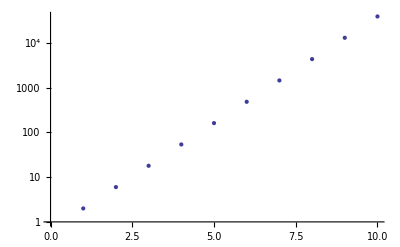

```mathematica
ListLogPlot[
Table[(3^n-3^(n-1)),{n,1,10}]
]
```

```mathematica
calc2=ReadList[FileNameForTupleBis[{3,31,43,173,229}]]
```

{«1»}

```mathematica
calc3=Take[GoodForTuple[{3,31,43,173,229}],5943]
```

{0,«5942»}

```mathematica
Length[calc2]
```

5943

```mathematica
Module[
{pos,calc2=ReadList[FileNameForTupleBis[{3,31,43,173,229}]],calc3=Take[GoodForTuple[{3,31,43,173,229}],5943]},
For[pos=1,pos<Length[calc3]-1,pos++,
If[calc2[[pos]]≠ calc3[[pos+1]],
Print[{calc2[[pos]], calc3[[pos+1]]}];
Break[]
]
]
]
```

{619936077624883545698997398859449791259575817655063735521634080436608973540529832537804126333470397809634646466801897806201836734788743382777517084078186751282776932470359234305521502440236092893569758603,1}

```mathematica
calc2[[1]]
```

619936077624883545698997398859449791259575817655063735521634080436608973540529832537804126333470397809634646466801897806201836734788743382777517084078186751282776932470359234305521502440236092893569758603

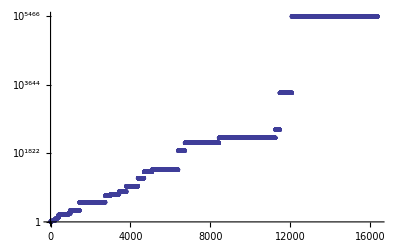

```mathematica
ListLogPlot[ReadList [FileNameForTupleBis[{3,31,43,173,229}]]]
```

```mathematica
DigitRatio[list_,digit_]:= Length[Select[list,#==digit&]]/Length[list]
```

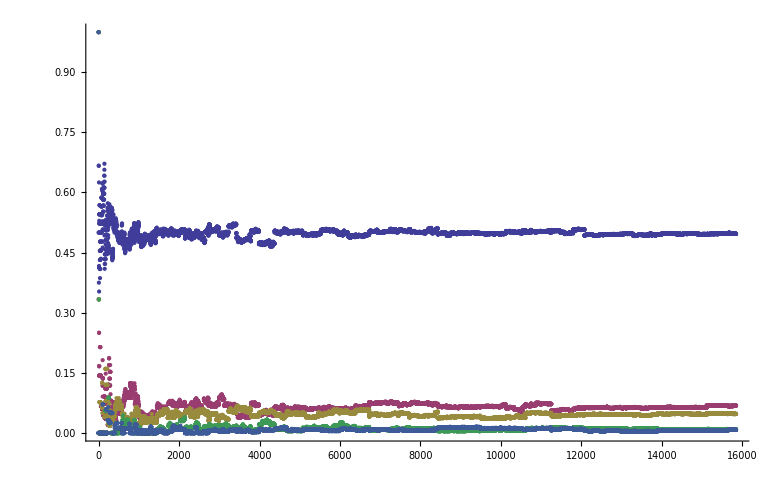

```mathematica
With[
{tuple={3,31,43,173,229}},
With[
{all=ReadList [FileNameForTupleBis[tuple]]},
ListPlot[
Table[
Table[
DigitRatio[IntegerDigits[v,p],1],{v,all}
],
{p,tuple}
]
]
]
]
```

```mathematica
DigitRatio[{1,2,3,1},1]
```

1/2